```mathematica
Quit;
ClearAll;
Needs["VariationalMethods`"]
$HistoryLength=1;
```

```mathematica
Action=Sqrt[r[x]^2(r[x]^2+2r'[x]v'[x]-(r[x]^2-m[v[x]]/r[x])v'[x]^2)]; (*Action functional (eqn4.5)*)
```

```mathematica
FullSimplify[Eliminate[{EulerEquations[Action,v[x],x],EulerEquations[Action,r[x],x],r[x]^4/r0^2==r[x]^2+2 r'[x] v'[x]-((-m[v[x]])/r[x]+r[x]^2) v'[x]^2},m[v[x]]]] ;(*We can eliminate one of the two EL equations using eqn4.6 which can be derived from reparametrrising the action in terms of v and then minimising*)
```

```mathematica
(*This function does the following: takes arguments r0,t,b,Col, where Col defines the Line colour of the output figures.
1. Produce a inital solution Sol to calculate ℓ/2
2. Produce SolL, i.e. the solution for v,r running from -ℓ/2 to -x0
3. Produce 3 plots of the geodesics in the rx,vx,rv planes, output as a list {rx,vx,rv}
4.Integrate to find geodesic length*)
yL=1;
f[r0_,t_,b_,Col_]:=Module[{a,m0,Eqn1,Eqn2,r,x,v,rmax,xmax,x0,Sol,ℓ,SolL,gr1,gr2,gr3,LInt,dot,scal,gr4,temp1,AH,y,surplot,ab},
a=1/3;
m0=1;
m[v_]:=m0(Tanh[v/a]+1)/2; (*define the mass function*)
Eqn1=r0^2(r[x]^2+2r'[x]v'[x]-(r[x]^2-m[v[x]]/r[x])v'[x]^2)-r[x]^4;
Eqn2=r[x]^3/r0^2+(6 r'[x] v'[x])/r[x]-3 r[x] (-1+v'[x]^2)-2 v''[x];
rmax=100;
x0=1/3 r0^2/rmax^3;
xmax=100;
Sol=NDSolve[{Eqn1==0,Eqn2==0,r[x0]==rmax,v[x0]==t-1/rmax+b/(2 rmax^2),v'[x0]==-rmax^2/r0^2+(b*rmax)/r0^2},{r,v},{x,x0,xmax}];
ℓ=2*x/.Last[Quiet[FindMinimum[v[x]/.Sol,{x,x0,x0,xmax}]]];
SolL=NDSolve[{Eqn1==0,Eqn2==0,r[-ℓ/2]==rmax,v[-ℓ/2]==t-1/rmax+b/(2 rmax^2),v'[-ℓ/2]==-rmax^2/r0^2+(b*rmax)/r0^2},{r,v},{x,-ℓ/2,-x0},"ExtrapolationHandler"->{Indeterminate &}];
gr1=Plot[{Evaluate[r[x]/.SolL],Evaluate[m[v[x]]^(1/3)/.SolL]},{x,-ℓ/2,ℓ/2},PlotStyle->{Col,{Dashed,Black}},PlotRange->All];
gr2=Plot[Evaluate[v[x]/.SolL],{x,-ℓ/2,ℓ/2},PlotStyle->{Col},PlotRange->All];
gr3=ParametricPlot[{Evaluate[{v[x],r[x]}/.SolL],Evaluate[{v[x],m[v[x]]^(1/3)}/.SolL]},{x,-ℓ/2,-x0},AspectRatio->1/GoldenRatio,PlotRange->All,PlotStyle->{Col,{Black,Dashed}}];
LInt=(2yL)/r0*(NIntegrate[r[x]^3/.SolL,{x,-ℓ/2,-x0}])-2yL*rmax;
gr4=ParametricPlot3D[Evaluate[{x,v[x],r[x]}/.SolL],{x,-ℓ/2,-x0},PlotRange->All,PlotStyle->Col];
AH=ParametricPlot3D[Evaluate[{y,v[x],m[v[x]]^(1/3)}/.SolL],{x,-ℓ/2,-x0},{y,-ℓ/2,ℓ/2},PlotRange->All,PlotStyle->{LightBlue,Opacity[0.5]}];
ab=ParametricPlot3D[Evaluate[{y,x,r[x]}/.SolL],{x,-ℓ/2,-x0},{y,0,yL},PlotRange->All,PlotStyle->None] ;
surplot=Show[{ab},{ab}/.L_Line:>{GeometricTransformation[L,ReflectionTransform[{0,1,0}]]},PlotRange->{{0,yL},{-ℓ/2,ℓ/2},{0,4}}];
{gr1,gr2,gr3,ℓ,LInt,gr4,AH,surplot}
]
```

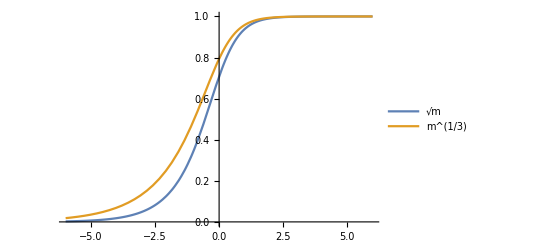

```mathematica
Plot[{((Tanh[x]+1)/2)^(1/2),((Tanh[x]+1)/2)^(1/3)},{x,-6,6},PlotLegends->{m^(1/2),m^(1/3)}]
```

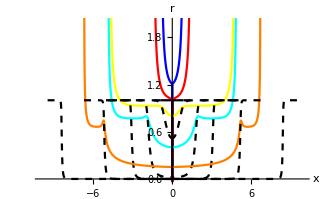

```mathematica
(*Create multiple plots with varying parameters*)
rx1=Part[Quiet[f[1.2,6,97.9223,Blue]],1];
rx2=Part[Quiet[f[1.0,6,98.2686945,Red]],1];
rx3=Part[Quiet[f[0.8,6,98.6151923084,Yellow]],1];
rx4=Part[Quiet[f[0.4,6,99.307794019324,Cyan]],1];
rx5=Part[Quiet[f[0.2,6,99.6539256341676,Purple]],1];
rx6=Part[Quiet[f[0.15,6,99.7404475500251,Orange]],1];
rx7=Part[Quiet[f[0.1,6,99.8269666440384,Pink]],1];
(*Stick the plots together then mirror each plot in the x=0 plane*)
Show[{rx1,rx2,rx3,rx4,rx5,rx6,rx7},{rx1,rx2,rx3,rx4,rx5,rx6,rx7}/.L_Line:>{GeometricTransformation[L,ReflectionTransform[{1,0}]]},PlotRange->{{-10,10},{0.0,2.0}},AxesLabel->{"x","r"},AxesOrigin->{0,0}]
```

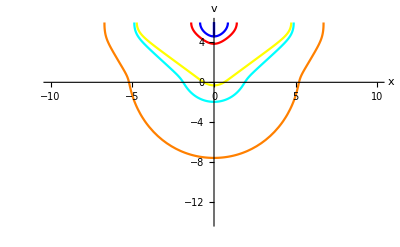

```mathematica
vx1=Part[Quiet[f[1.2,6,97.9223,Blue]],2];
vx2=Part[Quiet[f[1.0,6,98.2686945,Red]],2];
vx3=Part[Quiet[f[0.8,6,98.6151923084,Yellow]],2];
vx4=Part[Quiet[f[0.4,6,99.307794019324,Cyan]],2];
vx5=Part[Quiet[f[0.2,6,99.6539256341676,Purple]],2];
vx6=Part[Quiet[f[0.15,6,99.7404475500251,Orange]],2];
vx7=Part[Quiet[f[0.1,6,99.8269666440384,Pink]],2];

Show[{vx1,vx2,vx3,vx4,vx5,vx6,vx7},{vx1,vx2,vx3,vx4,vx5,vx6,vx7}/.L_Line:>{GeometricTransformation[L,ReflectionTransform[{1,0}]]},PlotRange->{{-10,10},{-14,6}},AxesOrigin->{0,0},AxesLabel->{"x","v"}]
```

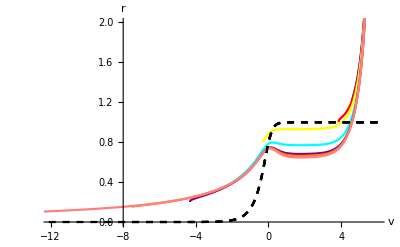

```mathematica
rv1=Part[Quiet[f[1.2,6,97.9223,Blue]],3];
rv2=Part[Quiet[f[1.0,6,98.2686945,Red]],3];
rv3=Part[Quiet[f[0.8,6,98.6151923084,Yellow]],3];
rv4=Part[Quiet[f[0.4,6,99.307794019324,Cyan]],3];
rv5=Part[Quiet[f[0.2,6,99.6539256341676,Purple]],3];
rv6=Part[Quiet[f[0.15,6,99.7404475500251,Orange]],3];
rv7=Part[Quiet[f[0.1,6,99.8269666440384,Pink]],3];

Show[{rv1,rv2,rv3,rv4,rv5,rv6,rv7},PlotRange->{{-12,6},{0.0,2.0}},AxesOrigin->{-8,0},AxesLabel->{"v","r"}]
```

```mathematica
xrv1=Part[Quiet[f[1.2,6,97.9223,Blue]],6];
xrv2=Part[Quiet[f[1.0,6,98.2686945,Red]],6];
xrv3=Part[Quiet[f[0.8,6,98.6151923084,Yellow]],6];
xrv4=Part[Quiet[f[0.4,6,99.307794019324,Cyan]],6];
xrv5=Part[Quiet[f[0.2,6,99.6539256341676,Purple]],6];
xrv6=Part[Quiet[f[0.15,6,99.7404475500251,Orange]],6];
xrv7=Part[Quiet[f[0.1,6,99.8269666440384,Pink]],6];
AHP=Part[Quiet[f[0.1,6,99.8269666440384,Pink]],7];

Show[{xrv1,xrv2,xrv3,xrv4,xrv5,xrv6,xrv7},{xrv1,xrv2,xrv3,xrv4,xrv5,xrv6,xrv7}/.L_Line:>{GeometricTransformation[L,ReflectionTransform[{1,0,0}]]},AHP,PlotRange->{{-10,10},{-14,6},{0.0,2.0}},BoxRatios->{1, 1, 1},AxesLabel->{"x","v","r"}]
```

-Graphics3D-

```mathematica
Quiet[Part[f[0.8,6,98.6151923084,Pink],8]]
```

-Graphics3D-

```mathematica
(*Begin Horrible List*)
(*t=0*)
Quiet[gl10=Flatten[f[10,0,82.82,Blue][[{4,5}]],1];
gl11=Flatten[f[3,0,94.807,Blue][[{4,5}]],1];
gl0=Flatten[f[2,0,96.537,Blue][[{4,5}]],1];
gl12=Flatten[f[1.5,0,97.4025,Blue][[{4,5}]],1];
gl1=Flatten[f[1.2,0,97.922,Blue][[{4,5}]],1];
(*gl2=Flatten[f[1.0,0,98.2681,Red][[{4,5}]],1];*)
gl3=Flatten[f[0.8,0,98.6145,Yellow][[{4,5}]],1];]
```

```mathematica
Quiet[gl13=Flatten[f[0.6,0,98.96077526,Yellow][[{4,5}]],1];
gl4=Flatten[f[0.4,0,99.30717,Cyan][[{4,5}]],1];
gl5=Flatten[f[0.2,0,99.653615,Purple][[{4,5}]],1];
gl6=Flatten[f[0.15,0,99.74021,Orange][[{4,5}]],1];
gl7=Flatten[f[0.1,0,99.826804,Pink][[{4,5}]],1];
gl8=Flatten[f[0.01,0,99.9826803,Pink][[{4,5}]],1];
gl9=Flatten[f[0.001,0,99.998268018,Blue][[{4,5}]],1];]
Lt0=ListCurvePathPlot[{ gl10,gl11,gl12,gl13,gl0,gl1,gl3,gl4,gl5,gl6,gl7,gl8,gl9},AxesLabel->{"ℓ","Ã(ℓ,t)"},PlotRange->All,AxesOrigin->{0,0},InterpolationOrder->3,PlotStyle->{Green}];
```

```mathematica
(*t=2*)
Quiet[
gl0=Flatten[f[10,2,82.82,Blue][[{4,5}]],1];
gl1=Flatten[f[3,2,94.807,Blue][[{4,5}]],1];gl2=Flatten[f[2,2,96.5373,Blue][[{4,5}]],1];
gl3=Flatten[f[1.5,2,97.40233,Blue][[{4,5}]],1];
gl4=Flatten[f[1.2,2,97.9223,Blue][[{4,5}]],1];
gl5=Flatten[f[1.0,2,98.26872,Red][[{4,5}]],1];
gl6=Flatten[f[0.8,2,98.61519,Yellow][[{4,5}]],1];
gl7=Flatten[f[0.6,2,98.961535,Yellow][[{4,5}]],1];]
```

```mathematica
Quiet[
gl8=Flatten[f[0.4,2,99.307765,Cyan][[{4,5}]],1];gl9=Flatten[f[0.2,2,99.653906,Purple][[{4,5}]],1];
gl10=Flatten[f[0.15,2,99.74043225,Orange][[{4,5}]],1];
gl11=Flatten[f[0.1,2,99.826956,Pink][[{4,5}]],1];
gl12=Flatten[f[0.08,2,99.8615645,Pink][[{4,5}]],1];
gl13=Flatten[f[0.01,2,99.98269561,Pink][[{4,5}]],1];]

Lt2=ListCurvePathPlot[{ gl10,gl0,gl1,gl2,gl3,gl4,gl5,gl6,gl7,gl8,gl9,gl11,gl12,gl13},AxesLabel->{"ℓ","Ã(ℓ,t)"},PlotRange->All,AxesOrigin->{0,0},InterpolationOrder->3,PlotStyle->{Cyan}];
```

```mathematica
(*t=4*)
Quiet[gl0=Flatten[f[10,4,82.82,Blue][[{4,5}]],1];
gl1=Flatten[f[3,4,94.804979,Blue][[{4,5}]],1];
gl2=Flatten[f[2,4,96.5369,Blue][[{4,5}]],1];
gl3=Flatten[f[1.5,4,97.4026,Blue][[{4,5}]],1];
gl4=Flatten[f[1.2,4,97.9223,Blue][[{4,5}]],1];
gl5=Flatten[f[1.0,4,98.268691,Red][[{4,5}]],1];
gl6=Flatten[f[0.8,4,98.6151923,Yellow][[{4,5}]],1];]
```

```mathematica
Quiet[
gl7=Flatten[f[0.6,4,98.96156074,Yellow][[{4,5}]],1];gl8=Flatten[f[0.4,4,99.30779398,Cyan][[{4,5}]],1];gl9=Flatten[f[0.2,4,99.6539256105,Purple][[{4,5}]],1];
gl10=Flatten[f[0.15,4,99.740447531,Orange][[{4,5}]],1];
gl11=Flatten[f[0.1,4,99.826966631,Pink][[{4,5}]],1];
gl12=Flatten[f[0.01,4,99.982696792465,Pink][[{4,5}]],1];]
```

```mathematica
Lt4=ListCurvePathPlot[{ gl0,gl1,gl2,gl3,gl4,gl5,gl6,gl7,gl8,gl9,gl10,gl11,gl12},AxesLabel->{"ℓ","Ã(ℓ,t)"},PlotRange->All,AxesOrigin->{0,0},InterpolationOrder->3,PlotStyle->{Purple}];
```

```mathematica
(*t=6*)
Quiet[
gl0=Flatten[f[10,6,82.8215,Blue][[{4,5}]],1];
gl1=Flatten[f[3,6,94.807,Blue][[{4,5}]],1];
gl2=Flatten[f[2,6,96.537,Blue][[{4,5}]],1];
gl3=Flatten[f[1.5,6,97.403001,Blue][[{4,5}]],1];
gl4=Flatten[f[1.2,6,97.9223,Red][[{4,5}]],1];
gl5=Flatten[f[1.0,6,98.26869175,Red][[{4,5}]],1];
gl6=Flatten[f[0.95,6,98.355314,Red][[{4,5}]],1];]
```

```mathematica
Quiet[
gl7=Flatten[f[0.9,6,98.4419526646,Yellow][[{4,5}]],1];(*gl8=Flatten[f[0.8,6,98.6151923084,Yellow][[{4,5}]],1];*)
(*gl9=Flatten[f[0.4,6,99.307794019324,Cyan][[{4,5}]],1];*)
gl10=Flatten[f[0.2,6,99.6539256341665,Purple][[{4,5}]],1];gl11=Flatten[f[0.15,6,99.74044755002504,Orange][[{4,5}]],1];
gl12=Flatten[f[0.1,6,99.8269666440384,Pink][[{4,5}]],1];
gl13=Flatten[f[0.09,6,99.8442702019692,Pink][[{4,5}]],1];]
```

```mathematica
Lt6=ListCurvePathPlot[{ gl0,gl1,gl2,gl3,gl4,gl5,gl6,gl7,gl10,gl11,gl12,gl13},AxesLabel->{"ℓ","Ã(ℓ,t)"},PlotRange->All,AxesOrigin->{0,0},InterpolationOrder->3,PlotStyle->{Red}];
```

```mathematica
(*t=8*)
Quiet[gl0=Flatten[f[10,8,82.7669,Blue][[{4,5}]],1];
gl1=Flatten[f[3,8,94.8069,Blue][[{4,5}]],1];
gl2=Flatten[f[2,8,96.537,Blue][[{4,5}]],1];
(*gl3=Flatten[f[1.5,8,97.5367,Blue][[{4,5}]],1];*)
gl4=Flatten[f[1.2,8,97.922217,Red][[{4,5}]],1];
gl5=Flatten[f[1,8,98.2688,Red][[{4,5}]],1];
gl6=Flatten[f[0.9,8,98.4419487294695,Red][[{4,5}]],1]];
```

```mathematica
Quiet[gl7=Flatten[f[0.8,8,98.615192308431,Yellow][[{4,5}]],1];
gl8=Flatten[f[0.7,8,98.7883952618124,Yellow][[{4,5}]],1];
gl9=Flatten[f[0.6,8,98.9615607860103,Yellow][[{4,5}]],1];
(*gl10=Flatten[f[0.4,8,99.30779401936822,Cyan][[{4,5}]],1];*)
gl11=Flatten[f[0.3,8,99.48087006927932,Purple][[{4,5}]],1];]
Lt8=ListCurvePathPlot[{ gl0,gl1,gl2,gl4,gl5,gl6,gl7,gl8,gl9,gl11},PlotRange->All,AxesOrigin->{0,0},InterpolationOrder->3,PlotStyle->{Blue}];
(*End Horrible list*)
```

```mathematica
Lt8=ListCurvePathPlot[{ gl0,gl1,gl2,gl4,gl5,gl6,gl7,gl8,gl9,gl11},PlotRange->All,AxesOrigin->{0,0},InterpolationOrder->3,PlotStyle->{Blue}]
```

-Graphics-

```mathematica
(*Complile all graphs*)
(*numerically solve for AdS4-Schwarzchild thermal result*)
m=1;
rmax=100;
Action=Sqrt[r^2/(r^2-m/r)+r^4 x'[r]^2];
A[r0_]:=2yL(NIntegrate[Action/.NDSolve[{x'[r]==√(r0^4/(r^2(r^2-m/r)(r^4-r0^4))),x[rmax]==0.01},x,{r,r0,rmax}],{r,r0,rmax}]-rmax)
ℓ[r0_]:=2yL*Abs[x[r0]/.NDSolve[{x'[r]==√(r0^4/(r^2(r^2-m/r)(r^4-r0^4))),x[rmax]==0.01},x,{r,r0,rmax}]]
TherTable=Quiet[Partition[Flatten[Table[{ℓ[r0],A[r0]},{r0,1,15,0.1}],2],2]];
TherRes=ListLinePlot[{TherTable},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Black,Dashed}];
VacRes=Plot[yL(-(4Pi/ℓ)(Gamma[3/4]/Gamma[1/4])^2),{ℓ,0,60},PlotStyle->{Black, DotDashed},PlotRange->All];
```

```mathematica
Show[{VacRes,TherRes,Lt0,Lt2,Lt4,Lt6,Lt8},PlotRange->{{0,20},{-40,20}},AxesLabel->{"ℓ","Ã(ℓ,t)"},AspectRatio->1]
```

-Graphics-